# Calculation of z expansion axial form factor

Victoria Parrish and Kevin McFarland, July 2018
Tejin Cai and Kevin McFarland, spring 2021.

This version is derived from Tejin’s v3.03 (April 30)

## Definition of the z expansion and the list of parameters.

D2 fits of Aaron S . Meyer, Minerba Betancourt, Richard Gran, and Richard J . Hill, Phys . Rev . D 93, 113015 used nine terms (a0 ... a8).

This code has been generalized to an arbitrary number of terms based on the length of the list (aList) below. 
aList must be of the form a0, a1 ..., a_ (Length - 1)
The notebook must be re-evaluated if aList is changed here.

```mathematica
aListMeyer={a0,a1,a2,a3,a4,a5,a6,a7,a8}
```

{a0,a1,a2,a3,a4,a5,a6,a7,a8}

### User choice: selection of the number of parameters in aList

Here are some possible versions.  Note that these are all disabled for executive, so copy the text, not the cell!

#### For one free parameter

```mathematica
aList={a0,a1,a2,a3,a4,a5}
```

#### For two free parameters

```mathematica
aList={a0,a1,a2,a3,a4,a5,a6}
```

#### For three free parameters

```mathematica
aList={a0,a1,a2,a3,a4,a5,a6,a7}
```

#### For four free parameters (Meyer et al default)

```mathematica
aList={a0,a1,a2,a3,a4,a5,a6,a7,a8}
```

#### For five free parameters

```mathematica
aList={a0,a1,a2,a3,a4,a5,a6,a7,a8,a9}
```

#### Here is the user choice of aList.

```mathematica
aList={a0,a1,a2,a3,a4,a5,a6,a7,a8}
```

{a0,a1,a2,a3,a4,a5,a6,a7,a8}

## Definition of z expansion function

```mathematica
zExp[aList_,z_]:=aList.Table[z^n,{n,0,Length[aList]-1}]
```

## Constraint terms

Following Meyer, here are the terms in the k expansion (four of them).  Eqn (16)

```mathematica
constraints[aList_]:= (Total[aList]==0)&&(aList.Table[n,{n,0,Length[aList]-1}]==0)&&(aList.Table[n(n-1),{n,0,Length[aList]-1}]==0)&&(aList.Table[n(n-1)(n-2),{n,0,Length[aList]-1}]==0)
```

```mathematica
constraints[aList]
```

a0+a1+a2+a3+a4+a5+a6+a7+a8==0&&a1+2 a2+3 a3+4 a4+5 a5+6 a6+7 a7+8 a8==0&&2 a2+6 a3+12 a4+20 a5+30 a6+42 a7+56 a8==0&&6 a3+24 a4+60 a5+120 a6+210 a7+336 a8==0

#### FA0 constraint must be implemented after definition of t0

```mathematica
FA0=-1.2723
```

-1.2723

## Read in data

Current choice is tejinBBBA07CV

```mathematica
tejinBBBA07CVfile=FileNameJoin[{NotebookDirectory[],"tables/Fa_BBBA07_Orig.csv"}];data=Import[tejinBBBA07CVfile][[5;;-3,1;;2]]/.{x_,y_}->{x,y/FA0};
data//MatrixForm
```

(0.01875 | 1.13398
0.03125 | 0.546563
0.04375 | 0.254993
0.075 | 0.797907
0.125 | 0.776817
0.175 | 0.748745
0.25 | 0.745496
0.3499 | 0.613
0.4995 | 0.395592
0.6993 | 0.304909
0.8991 | 0.285931
1.099 | 0.2751
1.582 | 0.225692
2.815 | 0.209177
4.768 | 0.248873)

```mathematica
tejinBBBA07Covfile=FileNameJoin[{NotebookDirectory[],"tables/Cov_BBBA07_Orig.csv"}];covarianceData=Import[tejinBBBA07Covfile][[4;;-3,4;;-3]]/FA0^2;tejinBBBA07Covfile;
covarianceData//MatrixForm
```

(0.439831 | 0.043759 | -0.0835704 | 0.00552703 | 0.0133804 | 0.0098048 | 0.00525664 | 0.00551194 | 0.0104216 | 0.00913997 | 0.00704076 | 0.00549121 | 0.00220219 | 0.000654443 | 0.00085575
0.043759 | 0.375345 | 0.327114 | 0.0163374 | 0.0105199 | 0.0159408 | 0.00887126 | 0.0064278 | 0.00854277 | 0.00920668 | 0.00831528 | 0.00800428 | 0.00501876 | 0.00192979 | -0.00120004
-0.0835704 | 0.327114 | 1.14154 | 0.111402 | 0.0181893 | 0.0192675 | 0.00913587 | 0.00588362 | 0.016517 | 0.012068 | 0.00573931 | 0.00619071 | 0.0014433 | -0.00110883 | -0.00429943
0.00552703 | 0.0163374 | 0.111402 | 0.0674632 | 0.0107492 | 0.00287043 | 0.0025997 | 0.00312512 | 0.00528765 | 0.00400217 | 0.00196094 | 0.0015853 | 0.000606824 | -0.000276321 | -0.0000581419
0.0133804 | 0.0105199 | 0.0181893 | 0.0107492 | 0.0199371 | 0.0082311 | 0.00256564 | 0.00275326 | 0.0042443 | 0.00362657 | 0.00262613 | 0.00238074 | 0.00122516 | 0.00038338 | -0.000531655
0.0098048 | 0.0159408 | 0.0192675 | 0.00287043 | 0.0082311 | 0.0128778 | 0.00461281 | 0.00201058 | 0.0035486 | 0.00357728 | 0.00276018 | 0.00271279 | 0.00140651 | 0.000577894 | -0.00130686
0.00525664 | 0.00887126 | 0.00913587 | 0.0025997 | 0.00256564 | 0.00461281 | 0.00589504 | 0.00258144 | 0.0020374 | 0.0028772 | 0.00269634 | 0.0023224 | 0.00136729 | 0.000671934 | -0.000138705
0.00551194 | 0.0064278 | 0.00588362 | 0.00312512 | 0.00275326 | 0.00201058 | 0.00258144 | 0.00532522 | 0.00281344 | 0.00208691 | 0.00227451 | 0.00195377 | 0.0013125 | 0.000619834 | 0.000562877
0.0104216 | 0.00854277 | 0.016517 | 0.00528765 | 0.0042443 | 0.0035486 | 0.0020374 | 0.00281344 | 0.00860402 | 0.00512919 | 0.00323259 | 0.0026999 | 0.00152989 | 0.000746219 | 0.0000686364
0.00913997 | 0.00920668 | 0.012068 | 0.00400217 | 0.00362657 | 0.00357728 | 0.0028772 | 0.00208691 | 0.00512919 | 0.0115496 | 0.00679095 | 0.00336749 | 0.00196284 | 0.00110178 | 0.000210917
0.00704076 | 0.00831528 | 0.00573931 | 0.00196094 | 0.00262613 | 0.00276018 | 0.00269634 | 0.00227451 | 0.00323259 | 0.00679095 | 0.0107456 | 0.006348 | 0.00197467 | 0.000906349 | 0.000492832
0.00549121 | 0.00800428 | 0.00619071 | 0.0015853 | 0.00238074 | 0.00271279 | 0.0023224 | 0.00195377 | 0.0026999 | 0.00336749 | 0.006348 | 0.00785887 | 0.00246874 | 0.000312949 | -0.0000267111
0.00220219 | 0.00501876 | 0.0014433 | 0.000606824 | 0.00122516 | 0.00140651 | 0.00136729 | 0.0013125 | 0.00152989 | 0.00196284 | 0.00197467 | 0.00246874 | 0.00325709 | 0.000508104 | -0.0000432193
0.000654443 | 0.00192979 | -0.00110883 | -0.000276321 | 0.00038338 | 0.000577894 | 0.000671934 | 0.000619834 | 0.000746219 | 0.00110178 | 0.000906349 | 0.000312949 | 0.000508104 | 0.00199687 | 0.0000392246
0.00085575 | -0.00120004 | -0.00429943 | -0.0000581419 | -0.000531655 | -0.00130686 | -0.000138705 | 0.000562877 | 0.0000686364 | 0.000210917 | 0.000492832 | -0.0000267111 | -0.0000432193 | 0.0000392246 | 0.0144277)

```mathematica
corrData=Table[covarianceData[[i,j]]/Sqrt[covarianceData[[i,i]]covarianceData[[j,j]]],{i,Length[data]},{j,Length[data]}];corrData//MatrixForm
```

(1. | 0.107698 | -0.117941 | 0.032086 | 0.142888 | 0.130279 | 0.103234 | 0.113892 | 0.16941 | 0.128239 | 0.102414 | 0.0933997 | 0.058183 | 0.0220828 | 0.0107425
0.107698 | 1. | 0.499734 | 0.102668 | 0.121609 | 0.229285 | 0.188593 | 0.143773 | 0.150326 | 0.139832 | 0.130932 | 0.147376 | 0.143538 | 0.0704889 | -0.0163074
-0.117941 | 0.499734 | 1. | 0.401435 | 0.12057 | 0.158913 | 0.111368 | 0.0754622 | 0.166661 | 0.105101 | 0.0518201 | 0.0653604 | 0.0236698 | -0.0232244 | -0.0335017
0.032086 | 0.102668 | 0.401435 | 1. | 0.293099 | 0.0973854 | 0.130361 | 0.164878 | 0.219472 | 0.143377 | 0.0728308 | 0.068849 | 0.0409369 | -0.023807 | -0.00186362
0.142888 | 0.121609 | 0.12057 | 0.293099 | 1. | 0.513696 | 0.236658 | 0.267207 | 0.324059 | 0.238991 | 0.179419 | 0.190195 | 0.152036 | 0.0607607 | -0.0313473
0.130279 | 0.229285 | 0.158913 | 0.0973854 | 0.513696 | 1. | 0.529422 | 0.24279 | 0.337121 | 0.293326 | 0.23464 | 0.26966 | 0.217174 | 0.11396 | -0.0958758
0.103234 | 0.188593 | 0.111368 | 0.130361 | 0.236658 | 0.529422 | 1. | 0.460734 | 0.286076 | 0.348694 | 0.338778 | 0.341204 | 0.312034 | 0.195843 | -0.0150401
0.113892 | 0.143773 | 0.0754622 | 0.164878 | 0.267207 | 0.24279 | 0.460734 | 1. | 0.415641 | 0.266104 | 0.300679 | 0.302013 | 0.315149 | 0.190078 | 0.0642164
0.16941 | 0.150326 | 0.166661 | 0.219472 | 0.324059 | 0.337121 | 0.286076 | 0.415641 | 1. | 0.514536 | 0.336189 | 0.328335 | 0.288998 | 0.180028 | 0.00616035
0.128239 | 0.139832 | 0.105101 | 0.143377 | 0.238991 | 0.293326 | 0.348694 | 0.266104 | 0.514536 | 1. | 0.609582 | 0.353463 | 0.320027 | 0.229423 | 0.0163392
0.102414 | 0.130932 | 0.0518201 | 0.0728308 | 0.179419 | 0.23464 | 0.338778 | 0.300679 | 0.336189 | 0.609582 | 1. | 0.690782 | 0.333783 | 0.195661 | 0.0395808
0.0933997 | 0.147376 | 0.0653604 | 0.068849 | 0.190195 | 0.26966 | 0.341204 | 0.302013 | 0.328335 | 0.353463 | 0.690782 | 1. | 0.487956 | 0.0789983 | -0.0025085
0.058183 | 0.143538 | 0.0236698 | 0.0409369 | 0.152036 | 0.217174 | 0.312034 | 0.315149 | 0.288998 | 0.320027 | 0.333783 | 0.487956 | 1. | 0.199234 | -0.0063047
0.0220828 | 0.0704889 | -0.0232244 | -0.023807 | 0.0607607 | 0.11396 | 0.195843 | 0.190078 | 0.180028 | 0.229423 | 0.195661 | 0.0789983 | 0.199234 | 1. | 0.00730778
0.0107425 | -0.0163074 | -0.0335017 | -0.00186362 | -0.0313473 | -0.0958758 | -0.0150401 | 0.0642164 | 0.00616035 | 0.0163392 | 0.0395808 | -0.0025085 | -0.0063047 | 0.00730778 | 1.)

```mathematica
dataList=Table[{data[[i,1]],Around[data[[i,2]],Sqrt[covarianceData[[i,i]]]]},{i,Length[data]}]
```

{{0.01875,1.10.7},{0.03125,0.50.6},{0.04375,0.31.1},{0.075,0.800.26},{0.125,0.780.14},{0.175,0.750.11},{0.25,0.750.08},{0.3499,0.610.07},{0.4995,0.400.09},{0.6993,0.300.11},{0.8991,0.290.10},{1.099,0.280.09},{1.582,0.230.06},{2.815,0.210.04},{4.768,0.250.12}}

```mathematica
1/Diagonal[covarianceData]
```

{2.2736,2.66422,0.876008,14.8229,50.1577,77.6532,169.634,187.786,116.225,86.5834,93.0611,127.245,307.023,500.783,69.3112}

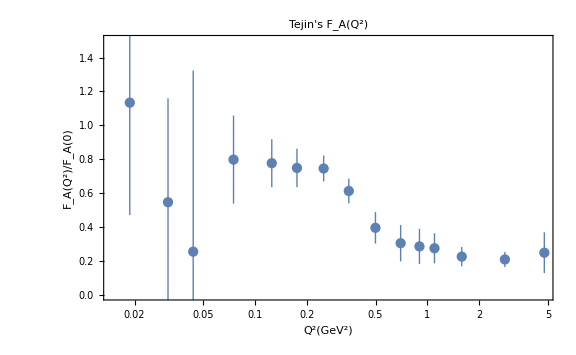

```mathematica
ListLogLinearPlot[{dataList},PlotRange->{0,1.5},LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"Q^2(GeV^2)","F_A(Q^2)/F_A(0)"},PlotLabel->"Tejin's F_A(Q^2)",ImageSize->Large]
```

## Definition of tcut and t0 parameters, to relate Q2 to z

### User choice of the parameters. t0, in particular, is useful for having a different z range to keep |z|.

Default Meyer et al paper choices

```mathematica
meyerChoices={t0->-.28,tcut->9 QuantityMagnitude[UnitConvert[Entity["Particle","PiPlus"]["Mass"],"GeV/c^2"]]^2}
```

{t0→-0.28,tcut→0.1753196}

An alternate choice in Meyer et al paper, higher t0

```mathematica
meyerAltChoices={t0->-.57,tcut->9 QuantityMagnitude[UnitConvert[Entity["Particle","PiPlus"]["Mass"],"GeV/c^2"]]^2}
```

{t0→-0.57,tcut→0.1753196}

“Optimized” to minimize uncertainty (by some metric; right now just balancing precise MINERvA data points on both sides of z=0)

```mathematica
optMINERvAchoices={t0->-.78,tcut->9 QuantityMagnitude[UnitConvert[Entity["Particle","PiPlus"]["Mass"],"GeV/c^2"]]^2}
```

{t0→-0.78,tcut→0.1753196}

#### Here is the user choice

```mathematica
choices={t0->-0.9,tcut->9 QuantityMagnitude[UnitConvert[Entity["Particle","PiPlus"]["Mass"],"GeV/c^2"]]^2}
```

{t0→-0.9,tcut→0.1753196}

```mathematica
{t0->-0.9,tcut->0.1753195965819489002}
```

{t0→-0.9,tcut→0.1753195965819489}

### Define z expansion after choices

```mathematica
theZ[Q2_]:=(Sqrt[tcut+Q2]-Sqrt[tcut-t0])/(Sqrt[tcut+Q2]+Sqrt[tcut-t0])/.choices
```

```mathematica
theQ2byZ=Simplify[InverseFunction[theZ]]
```

((7.05191×10^9+1.66036×10^10 #1) (3.90927×10^10+1.66036×10^10 #1))/(3.06309×10^20-6.12618×10^20 #1+3.06309×10^20 #1^2)&

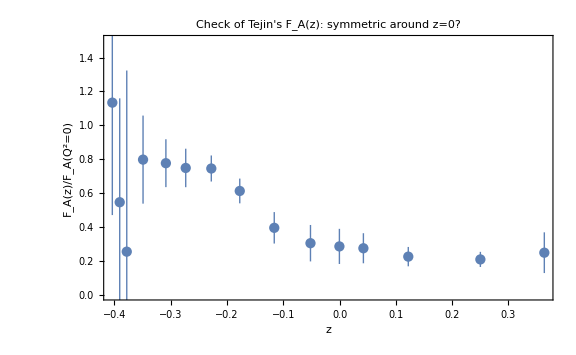

```mathematica
ListPlot[{theZ[#[[1]]],#[[2]]}&/@dataList,LabelStyle->{FontSize->16},PlotRange->{0,1.5},Frame->True,FrameLabel->{"z","F_A(z)/F_A(Q^2=0)"},PlotLabel->"Check of Tejin's F_A(z): symmetric around z=0?",ImageSize->Large]
```

```mathematica
theZMeyer[Q2_]:=(Sqrt[tcut+Q2]-Sqrt[tcut-t0])/(Sqrt[tcut+Q2]+Sqrt[tcut-t0])/.meyerChoices
```

```mathematica
theQ2byZMeyer=Simplify[InverseFunction[theZMeyer]]
```

((6.85456×10^8+2.92717×10^9 #1) (1.25002×10^10+2.92717×10^9 #1))/(3.06012×10^19-6.12023×10^19 #1+3.06012×10^19 #1^2)&

### Add the FA(0) constraint and solve for user choice

```mathematica
constraintFA0[aList_]:=(zExp[aList,theZ[0]]==FA0)
constrainedAs=Join[{First[aList]},aList[[-4;;-1]]]
freeAs=Complement[aList,constrainedAs]
```

{a0,a5,a6,a7,a8}

{a1,a2,a3,a4}

```mathematica
solution4 = First[Solve[constraints[aList]&&constraintFA0[aList], constrainedAs]]
```

{a0→-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4,a5→24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4,a6→-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4,a7→52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4,a8→-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4}

```mathematica
jacobian=D[zExp[aList,theZ[Q2]]/FA0/.solution4,#]&/@freeAs
```

{-0.785978 (-0.25504+(11.0736 (-1.03698+√(0.1753196+Q2))^8)/(1.03698+√(0.1753196+Q2))^8-(39.3952 (-1.03698+√(0.1753196+Q2))^7)/(1.03698+√(0.1753196+Q2))^7+(48.2944 (-1.03698+√(0.1753196+Q2))^6)/(1.03698+√(0.1753196+Q2))^6-(20.7178 (-1.03698+√(0.1753196+Q2))^5)/(1.03698+√(0.1753196+Q2))^5+(-1.03698+√(0.1753196+Q2))/(1.03698+√(0.1753196+Q2))),-0.785978 (-0.280115+(0.195988 (-1.03698+√(0.1753196+Q2))^8)/(1.03698+√(0.1753196+Q2))^8-(2.38624 (-1.03698+√(0.1753196+Q2))^7)/(1.03698+√(0.1753196+Q2))^7+(5.78395 (-1.03698+√(0.1753196+Q2))^6)/(1.03698+√(0.1753196+Q2))^6-(4.31358 (-1.03698+√(0.1753196+Q2))^5)/(1.03698+√(0.1753196+Q2))^5+(-1.03698+√(0.1753196+Q2))^2/(1.03698+√(0.1753196+Q2))^2),-0.785978 (-0.0752468+(1.36636 (-1.03698+√(0.1753196+Q2))^8)/(1.03698+√(0.1753196+Q2))^8-(5.97039 (-1.03698+√(0.1753196+Q2))^7)/(1.03698+√(0.1753196+Q2))^7+(9.46545 (-1.03698+√(0.1753196+Q2))^6)/(1.03698+√(0.1753196+Q2))^6-(5.78618 (-1.03698+√(0.1753196+Q2))^5)/(1.03698+√(0.1753196+Q2))^5+(-1.03698+√(0.1753196+Q2))^3/(1.03698+√(0.1753196+Q2))^3),-0.785978 (-0.0457281-(0.600485 (-1.03698+√(0.1753196+Q2))^8)/(1.03698+√(0.1753196+Q2))^8+(1.48738 (-1.03698+√(0.1753196+Q2))^7)/(1.03698+√(0.1753196+Q2))^7-(0.401938 (-1.03698+√(0.1753196+Q2))^6)/(1.03698+√(0.1753196+Q2))^6-(1.43922 (-1.03698+√(0.1753196+Q2))^5)/(1.03698+√(0.1753196+Q2))^5+(-1.03698+√(0.1753196+Q2))^4/(1.03698+√(0.1753196+Q2))^4)}

### Add the FA(0) constraint and solve for Meyer choice

```mathematica
constraintFA0Meyer[aList_]:=(zExp[aList,theZMeyer[0]]==FA0)
constrainedAsMeyer=Join[{First[aListMeyer]},aListMeyer[[-4;;-1]]]
freeAsMeyer=Complement[aListMeyer,constrainedAsMeyer]
```

{a0,a5,a6,a7,a8}

{a1,a2,a3,a4}

```mathematica
solution4Meyer = First[Solve[constraints[aListMeyer]&&constraintFA0Meyer[aListMeyer], constrainedAsMeyer]]
```

{a0→-1.19189+0.180606 a1-0.0729007 a2+0.00176715 a3-0.00653543 a4,a5→66.7457-45.1139 a1-15.9176 a2-10.099 a3-3.63402 a4,a6→-166.864+109.285 a1+34.7939 a2+20.2474 a3+5.08504 a4,a7→143.027-91.6727 a1-27.2519 a2-15.2121 a3-3.21575 a4,a8→-41.7161+26.3212 a1+7.44848 a2+4.06185 a3+0.77126 a4}

```mathematica
jacobianMeyer=D[zExp[aListMeyer,theZMeyer[Q2]]/FA0/.solution4Meyer,#]&/@freeAsMeyer
```

{-0.785978 (0.180606+(26.3212 (-0.674774+√(0.1753196+Q2))^8)/(0.674774+√(0.1753196+Q2))^8-(91.6727 (-0.674774+√(0.1753196+Q2))^7)/(0.674774+√(0.1753196+Q2))^7+(109.285 (-0.674774+√(0.1753196+Q2))^6)/(0.674774+√(0.1753196+Q2))^6-(45.1139 (-0.674774+√(0.1753196+Q2))^5)/(0.674774+√(0.1753196+Q2))^5+(-0.674774+√(0.1753196+Q2))/(0.674774+√(0.1753196+Q2))),-0.785978 (-0.0729007+(7.44848 (-0.674774+√(0.1753196+Q2))^8)/(0.674774+√(0.1753196+Q2))^8-(27.2519 (-0.674774+√(0.1753196+Q2))^7)/(0.674774+√(0.1753196+Q2))^7+(34.7939 (-0.674774+√(0.1753196+Q2))^6)/(0.674774+√(0.1753196+Q2))^6-(15.9176 (-0.674774+√(0.1753196+Q2))^5)/(0.674774+√(0.1753196+Q2))^5+(-0.674774+√(0.1753196+Q2))^2/(0.674774+√(0.1753196+Q2))^2),-0.785978 (0.00176715+(4.06185 (-0.674774+√(0.1753196+Q2))^8)/(0.674774+√(0.1753196+Q2))^8-(15.2121 (-0.674774+√(0.1753196+Q2))^7)/(0.674774+√(0.1753196+Q2))^7+(20.2474 (-0.674774+√(0.1753196+Q2))^6)/(0.674774+√(0.1753196+Q2))^6-(10.099 (-0.674774+√(0.1753196+Q2))^5)/(0.674774+√(0.1753196+Q2))^5+(-0.674774+√(0.1753196+Q2))^3/(0.674774+√(0.1753196+Q2))^3),-0.785978 (-0.00653543+(0.77126 (-0.674774+√(0.1753196+Q2))^8)/(0.674774+√(0.1753196+Q2))^8-(3.21575 (-0.674774+√(0.1753196+Q2))^7)/(0.674774+√(0.1753196+Q2))^7+(5.08504 (-0.674774+√(0.1753196+Q2))^6)/(0.674774+√(0.1753196+Q2))^6-(3.63402 (-0.674774+√(0.1753196+Q2))^5)/(0.674774+√(0.1753196+Q2))^5+(-0.674774+√(0.1753196+Q2))^4/(0.674774+√(0.1753196+Q2))^4)}

## Meyer fit with kmax=8, t0=-.27

```mathematica
meyerFitCorrelation={{1,0.350,-0.678,.611},{.35,1,-.898,0.367},{-.678,-.898,1,-.685},{.611,.367,-.685,1}}
```

{{1,0.35,-0.678,0.611},{0.35,1,-0.898,0.367},{-0.678,-0.898,1,-0.685},{0.611,0.367,-0.685,1}}

```mathematica
meyerCentralValue={a1->2.30, a2->-0.6,a3->-3.8,a4->2.3}
```

{a1→2.3,a2→-0.6,a3→-3.8,a4→2.3}

```mathematica
meyerUncertainties=DiagonalMatrix[{.13,1.0,2.5,2.7}]
```

{{0.13,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,2.5,0.},{0.,0.,0.,2.7}}

```mathematica
meyerCovariance=meyerUncertainties.meyerFitCorrelation.meyerUncertainties
```

{{0.0169,0.0455,-0.22035,0.214461},{0.0455,1.,-2.245,0.9909},{-0.22035,-2.245,6.25,-4.62375},{0.214461,0.9909,-4.62375,7.29}}

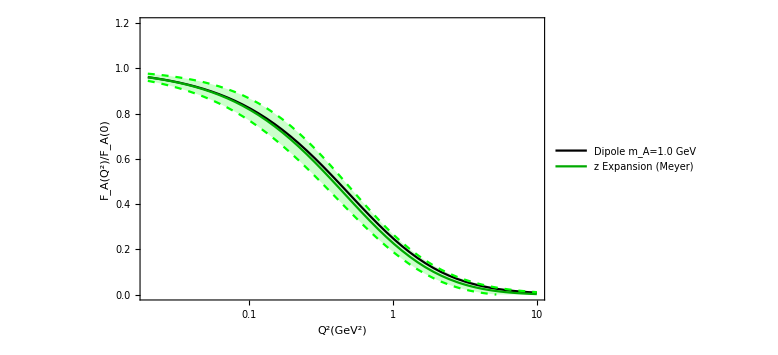

```mathematica
zExpMeyer=LogLinearPlot[{1/(1+Q2/1.00^2)^2,(zExp[aListMeyer,theZMeyer[Q2]]/FA0 /. solution4Meyer /.meyerCentralValue),(zExp[aListMeyer,theZMeyer[Q2]]/FA0  /. solution4Meyer /.meyerCentralValue)+Sqrt[jacobianMeyer.meyerCovariance.jacobianMeyer ],(zExp[aListMeyer,theZMeyer[Q2]]/FA0  /. solution4Meyer/.meyerCentralValue)-Sqrt[jacobianMeyer.meyerCovariance.jacobianMeyer] }, {Q2,0.02,10},PlotStyle->{Black,{Thick,Darker[Green]},{Dashed,Green},{Dashed,Green}},PlotRange->{0,1.2},Filling->{3->{4}},FillingStyle->{Opacity[0.2],Green},PlotLegends->{"Dipole m_A=1.0 GeV","z Expansion (Meyer)"},LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"Q^2(GeV^2)","F_A(Q^2)/F_A(0)"},ImageSize->Large]
```

## Fit to data from Tejin’s hydrogen analysis

### Use a chi2 minimization, with a penalty for poorly behaved expansion coefficients with a pre-factor of lambda.

```mathematica
Y=Table[zExp[aList,theZ[Q2]]/FA0 /. solution4,{Q2,data[[All,1]]}]
Y/.{a1->1.33574,a2->-1.03582,a3->0.277803,a4->0.064503}
dataModelDifference=Simplify[data[[All,2]]-Table[zExp[aList,theZ[Q2]]/FA0 /. solution4,{Q2,data[[All,1]]}]]
```

{-0.785978 (-0.403681 a1+0.162959 a2-0.0657833 a3-0.01072 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+0.000705194 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.00432744 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.0265555 a4-0.00174691 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.390537 a1+0.152519 a2-0.0595645 a3-0.00908475 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+0.000541129 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.00354793 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.0232622 a4-0.0013856 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.378019 a1+0.142898 a2-0.0540181 a3-0.00771909 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+0.000416971 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.00291796 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.0204199 a4-0.00110304 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.349091 a1+0.121865 a2-0.042542 a3-0.00518437 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+0.000220553 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.00180982 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.014851 a4-0.000631792 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.308495 a1+0.0951693 a2-0.0293593 a3-0.0027941 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+0.0000820328 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.000861967 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.00905719 a4-0.000265913 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.273258 a1+0.0746702 a2-0.0204043 a3-0.00152359 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+0.0000310877 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.000416334 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.00557563 a4-0.000113767 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.227814 a1+0.0518994 a2-0.0118234 a3-0.00061363 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+7.25522×10^-6 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.000139794 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.00269355 a4-0.000031847 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.177247 a1+0.0314166 a2-0.0055685 a3-0.000174943 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+9.74172×10^-7 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.0000310082 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.000987001 a4-5.49612×10^-6 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.115958 a1+0.0134463 a2-0.0015592 a3-0.0000209654 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+3.26893×10^-8 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+2.43111×10^-6 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.000180802 a4-2.81906×10^-7 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.0516002 a1+0.00266258 a2-0.000137389 a3-3.6581×10^-7 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+5.02584×10^-11 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+1.88759×10^-8 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+7.08932×10^-6 a4-9.73997×10^-10 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (-0.000209328 a1+4.38181×10^-8 a2-9.17234×10^-12 a3-4.01915×10^-19 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+3.6865×10^-30 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+8.41319×10^-23 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+1.92003×10^-15 a4-1.76111×10^-26 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (0.0424231 a1+0.00179972 a2+0.0000763499 a3+1.37409×10^-7 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+1.04911×10^-11 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+5.82931×10^-9 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+3.239×10^-6 a4+2.47297×10^-10 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (0.122179 a1+0.0149278 a2+0.00182387 a3+0.0000272265 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+4.96577×10^-8 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+3.32652×10^-6 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.00022284 a4+4.06432×10^-7 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (0.25026 a1+0.0626303 a2+0.0156739 a3+0.000981659 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+0.0000153864 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.00024567 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.00392255 a4+0.0000614816 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)),-0.785978 (0.363883 a1+0.132411 a2+0.0481822 a3+0.00637987 (24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)+0.000307396 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)+0.00232153 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)+1. (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)+0.0175327 a4+0.000844765 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4))}

{0.963297,0.940677,0.919361,0.870999,0.805341,0.750561,0.68307,0.612258,0.532528,0.45589,0.39974,0.35643,0.283004,0.184531,0.116067}

{0.301624-0.118688 a1-0.0326796 a2-0.0209448 a3-0.00668502 a4,-0.200598-0.177189 a1-0.0506751 a2-0.0311645 a3-0.0103772 a4,-0.422957-0.22333 a1-0.0662803 a2-0.0391619 a3-0.013568 a4,0.242914-0.300233 a1-0.0973575 a2-0.0523359 a3-0.0198186 a4,0.329364-0.355761 a1-0.13146 a2-0.0617624 a3-0.0262838 a4,0.353673-0.370824 a1-0.154198 a2-0.064586 a3-0.0301147 a4,0.384645-0.363165 a1-0.176595 a2-0.0644474 a3-0.0332149 a4,0.266876-0.335564 a1-0.194727 a2-0.0624659 a3-0.0349843 a4,0.0539983-0.291153 a1-0.209513 a2-0.060253 a3-0.0357766 a4,-0.0361649-0.241005 a1-0.21807 a2-0.0592485 a3-0.0359353 a4,-0.0551342-0.20062 a1-0.220164 a2-0.0591423 a3-0.0359413 a4,-0.0659628-0.167114 a1-0.21875 a2-0.0590829 a3-0.0359389 a4,-0.114996-0.104754 a1-0.208509 a2-0.0578097 a3-0.0357976 a4,-0.122537-0.012186 a1-0.173262 a2-0.0497317 a3-0.0339817 a4,-0.0502851+0.0463006 a1-0.128705 a2-0.0366493 a3-0.0292688 a4}

Here’s the penalty term as implemented in the Meyer et al analysis

```mathematica
penaltyLimits=Rest[aList]/Table[(Min[{5,25/k}] aList[[1]]),{k,1,Length[aList]-1}]
(*penaltyLimits=Rest[aList]/Table[aList[[1]]/k,{k,1,Length[aList]-1}]*)
```

{a1/(5 a0),a2/(5 a0),a3/(5 a0),a4/(5 a0),a5/(5 a0),(6 a6)/(25 a0),(7 a7)/(25 a0),(8 a8)/(25 a0)}

```mathematica
penaltyTerm=lambda(penaltyLimits.penaltyLimits)/.solution4
```

(a1^2/(25 (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)^2)+a2^2/(25 (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)^2)+a3^2/(25 (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)^2)+(24.3005-20.7178 a1-4.31358 a2-5.78618 a3-1.43922 a4)^2/(25 (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)^2)+(64 (-15.1878+11.0736 a1+0.195988 a2+1.36636 a3-0.600485 a4)^2)/(625 (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)^2)+(36 (-60.7513+48.2944 a1+5.78395 a2+9.46545 a3-0.401938 a4)^2)/(625 (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)^2)+a4^2/(25 (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)^2)+(49 (52.0725-39.3952 a1-2.38624 a2-5.97039 a3+1.48738 a4)^2)/(625 (-0.433938-0.25504 a1-0.280115 a2-0.0752468 a3-0.0457281 a4)^2)) lambda

```mathematica
lambda(penaltyLimits.penaltyLimits)
```

(a1^2/(25 a0^2)+a2^2/(25 a0^2)+a3^2/(25 a0^2)+a4^2/(25 a0^2)+a5^2/(25 a0^2)+(36 a6^2)/(625 a0^2)+(49 a7^2)/(625 a0^2)+(64 a8^2)/(625 a0^2)) lambda

```mathematica
chiSq=Simplify[dataModelDifference.Inverse[covarianceData].dataModelDifference+penaltyTerm]
```

(186.186+34.6701 a1^4+33.2703 a2^4+68.1798 a3+13.7086 a3^2+2.48712 a3^3+0.206231 a3^4+47.7093 a4+19.1231 a3 a4+4.82188 a3^2 a4+0.509882 a3^3 a4+6.63593 a4^2+3.13186 a3 a4^2+0.474926 a3^2 a4^2+0.680686 a4^3+0.197461 a3 a4^3+0.0309099 a4^4+a1^3 (48.4736+102.061 a2+29.9798 a3+17.0461 a4)+a2^3 (123.899+37.0207 a3+23.2085 a4)+7262.82 lambda-2006.16 a3 lambda+146.446 a3^2 lambda+215.654 a4 lambda-20.4861 a3 a4 lambda+5.26598 a4^2 lambda+a2^2 (221.927+15.545 a3^2+65.4049 a4+6.07739 a4^2+a3 (99.6987+19.3943 a4)+48.606 lambda)+a1^2 (-71.8386+126.303 a2^2+11.0057 a3^2+14.8539 a4+3.73046 a4^2+a3 (27.4428+12.7829 a4)+a2 (82.3041+74.5418 a3+43.3125 a4)+4393.64 lambda)+a2 (290.333+2.91703 a3^3+11.545 a4^2+0.707704 a4^3+a3^2 (27.0998+5.4332 a4)+a4 (76.4219-5.40827 lambda)-1060.16 lambda+a3 (109.615+35.302 a4+3.38906 a4^2+162.847 lambda))+a1 (17.641+91.8311 a2^3+2.22684 a3^3+3.96596 a4+4.90134 a4^2+0.493103 a4^3+a3^2 (12.307+4.01579 a4)+a2^2 (144.73+79.4125 a3+48.1391 a4)-11290.2 lambda-159.895 a4 lambda+a2 (15.215+22.9955 a3^2+53.1142 a4+8.4319 a4^2+a3 (83.4789+27.7529 a4)+838.083 lambda)+a3 (-0.0256584+15.3947 a4+2.42945 a4^2+1571.68 lambda)))/(1.70145+1. a1+1.09832 a2+0.29504 a3+0.179298 a4)^2

#### Note at this point, I could just give Tejin the chi2 function and he could do his own minimization!

#### L-curve analysis for the chi2 with penalty term

```mathematica
lcurveStudy={#[[1]],(FindMinimum[chiSq/.lambda->#,Partition[Riffle[freeAs,Prepend[Table[0,{i,1,Length[freeAs]-1}],1.5]],2]][[2]])}&/@Table[10^{n},{n,-5,3,.5}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

{{0.00001,{a1→1.44025,a2→-5.23627,a3→-0.122216,a4→23.0826}},{0.0000316228,{a1→1.42496,a2→-5.18696,a3→0.260488,a4→22.2668}},{0.0001,{a1→1.39089,a2→-5.07577,a3→1.10893,a4→20.4468}},{0.000316228,{a1→1.34125,a2→-4.89175,a3→2.32646,a4→17.7034}},{0.001,{a1→1.30246,a2→-4.62703,a3→3.22448,a4→14.9996}},{0.00316228,{a1→1.29075,a2→-4.18037,a3→3.33944,a4→12.4784}},{0.01,{a1→1.29816,a2→-3.44634,a3→2.77075,a4→9.41855}},{0.0316228,{a1→1.3095,a2→-2.52306,a3→1.86368,a4→5.80235}},{0.1,{a1→1.31613,a2→-1.71754,a3→1.04663,a4→2.63887}},{0.316228,{a1→1.32235,a2→-1.24533,a3→0.548748,a4→0.793779}},{1.,{a1→1.33574,a2→-1.03582,a3→0.277803,a4→0.064503}},{3.16228,{a1→1.35516,a2→-0.93075,a3→0.0902356,a4→-0.132866}},{10.,{a1→1.37221,a2→-0.823732,a3→-0.067642,a4→-0.182615}},{31.6228,{a1→1.38459,a2→-0.668895,a3→-0.224247,a4→-0.230957}},{100.,{a1→1.39446,a2→-0.484518,a3→-0.383765,a4→-0.292241}},{316.228,{a1→1.40187,a2→-0.327974,a3→-0.513865,a4→-0.345055}},{1000.,{a1→1.40611,a2→-0.23612,a3→-0.589559,a4→-0.375932}}}

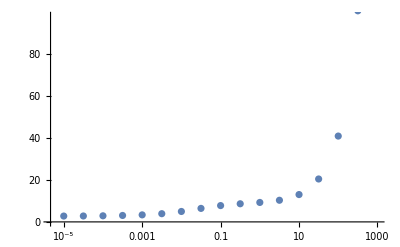

```mathematica
lcurve={#[[1]],chiSq/.#[[2]]/.lambda->#[[1]]}&/@lcurveStudy;ListLogLinearPlot[lcurve]
```

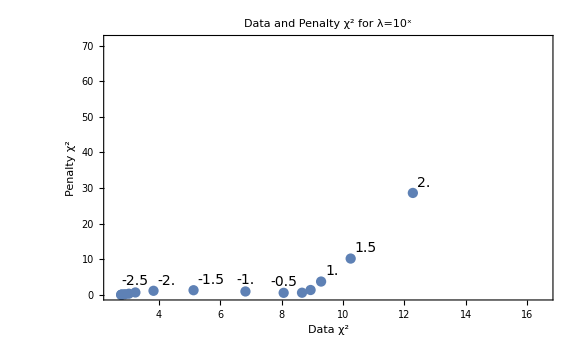

```mathematica
ListPlot[Labeled[{(chiSq-penaltyTerm)/.lambda->#[[1]]/.#[[2]],penaltyTerm/.lambda->#[[1]]/.#[[2]]},Log[10,#[[1]]]]&/@lcurveStudy,ImageSize->Large,Frame->True,LabelStyle->{FontSize->14},FrameLabel->{"Data χ^2","Penalty χ^2"},PlotLabel->"Data and Penalty χ^2 for λ=10^x"]
```

#### User choice to zoom in L-curve plot as needed

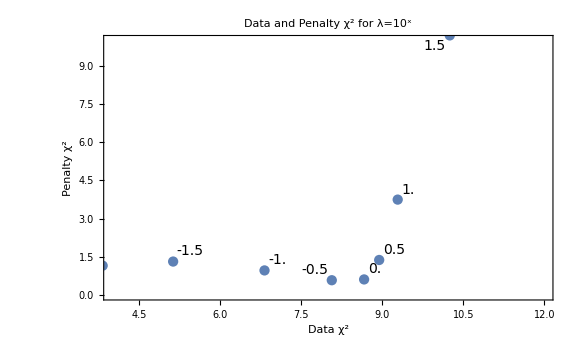

```mathematica
ListPlot[Labeled[{(chiSq-penaltyTerm)/.lambda->#[[1]]/.#[[2]],penaltyTerm/.lambda->#[[1]]/.#[[2]]},Log[10,#[[1]]]]&/@lcurveStudy,ImageSize->Large,Frame->True,LabelStyle->{FontSize->14},FrameLabel->{"Data χ^2","Penalty χ^2"},PlotLabel->"Data and Penalty χ^2 for λ=10^x",PlotRange->{{4,12},{0,10}}]
```

#### User choice of lambda

Note that the user will have to choose a different lambda for different numbers of parameters and datasets

```mathematica
aMin=FindMinimum[chiSq/.lambda->1,Partition[Riffle[freeAs,freeAs-freeAs],2]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{9.27063,{a1→1.33574,a2→-1.03582,a3→0.277803,a4→0.064503}}

### Obtain the covariance as Inverse[ 0.5 dchi/dxi dchi/dxj ]

```mathematica
generalCovChiSq=Inverse[Simplify[(1/2)*D[D[chiSq,{freeAs}],{freeAs}]]];
```

```mathematica
covChisq=generalCovChiSq/.lambda->1/.aMin[[2]];covChisq//MatrixForm
```

(0.0341918 | -0.00224855 | -0.169513 | 0.190947
-0.00224855 | 0.126474 | -0.088693 | -0.30677
-0.169513 | -0.088693 | 0.945482 | -0.698911
0.190947 | -0.30677 | -0.698911 | 2.21889)

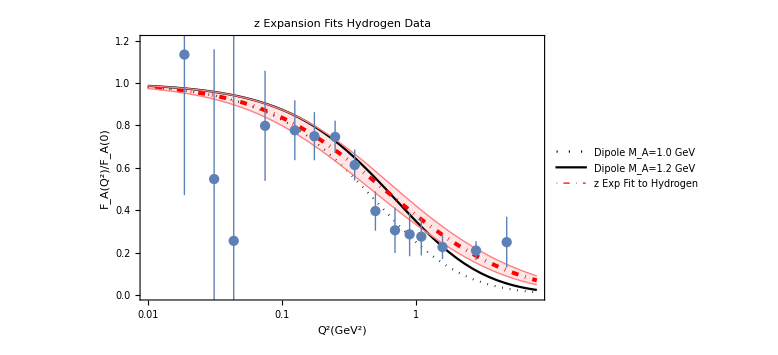

```mathematica
Show[LogLinearPlot[{1/(1+Q2/1.00^2)^2,1/(1+Q2/1.2^2)^2,(zExp[aList,theZ[Q2]] /FA0 /. solution4 /.aMin[[2]]) ,(zExp[aList,theZ[Q2]] /FA0 /. solution4 /.aMin[[2]])+Sqrt[jacobian.covChisq.jacobian ],(zExp[aList,theZ[Q2]] /FA0 /. solution4 /.aMin[[2]])-Sqrt[jacobian.covChisq.jacobian ]}, {Q2,0.01,8},PlotStyle->{{Dotted,Black},Black,{Thickness[.005],DotDashed,Red},{Thin,Pink},{Thin,Pink}},Filling->{4->{5}},FillingStyle->{Opacity[0.2],Pink},PlotRange->{0,1.2},PlotLegends->Placed[{"Dipole M_A=1.0 GeV","Dipole M_A=1.2 GeV","z Exp Fit to Hydrogen"},{.75,.8}],LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"Q^2(GeV^2)","F_A(Q^2)/F_A(0)"},ImageSize->Large,PlotLabel->"z Expansion Fits Hydrogen Data"],ListLogLinearPlot[{dataList}]]
```

```mathematica
FaDipole=1/(1+thisQ2/Ma^2)^2/.Ma->1.2;
ratioDataList=dataList/.{x_,y_}->{x,y/FaDipole/.thisQ2->x}
```

{{0.01875,1.20.7},{0.03125,0.60.6},{0.04375,0.31.1},{0.075,0.880.29},{0.125,0.920.17},{0.175,0.940.14},{0.25,1.030.11},{0.3499,0.950.11},{0.4995,0.720.17},{0.6993,0.670.24},{0.8991,0.750.27},{1.099,0.860.28},{1.582,0.990.25},{2.815,1.80.4},{4.768,4.62.2}}

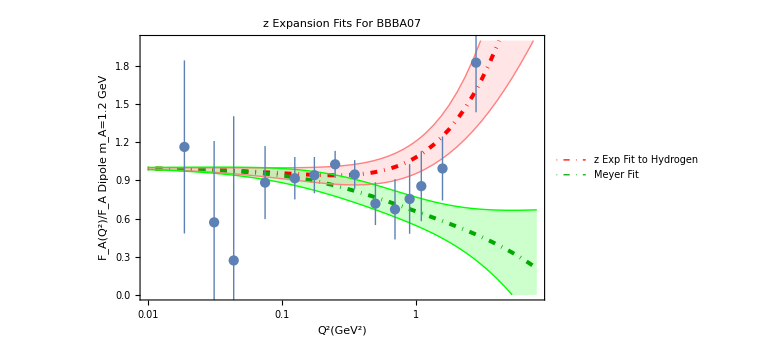

```mathematica
Show[LogLinearPlot[{(zExp[aList,theZ[Q2]] /FA0 /. solution4 /.aMin[[2]])/FaDipole/.thisQ2->Q2 ,
(zExp[aListMeyer,theZMeyer[Q2]] /FA0 /. solution4Meyer /.meyerCentralValue)/FaDipole/.thisQ2->Q2 ,
((zExp[aList,theZ[Q2]] /FA0 /. solution4 /.aMin[[2]])+Sqrt[jacobian.covChisq.jacobian ])/FaDipole/.thisQ2->Q2 ,((zExp[aList,theZ[Q2]] /FA0 /. solution4 /.aMin[[2]])-Sqrt[jacobian.covChisq.jacobian ])/FaDipole/.thisQ2->Q2,
( (zExp[aListMeyer,theZMeyer[Q2]] /FA0 /. solution4Meyer /.meyerCentralValue) +Sqrt[jacobianMeyer.meyerCovariance.jacobianMeyer ])/FaDipole/.thisQ2->Q2 ,((zExp[aListMeyer,theZMeyer[Q2]] /FA0 /. solution4Meyer /.meyerCentralValue) -Sqrt[jacobianMeyer.meyerCovariance.jacobianMeyer ])/FaDipole/.thisQ2->Q2
 }, {Q2,0.01,8},PlotStyle->{{Thickness[.005],DotDashed,Red},{Thickness[.005],DotDashed,Darker[Green]},{Thin,Pink},{Thin,Pink},{Thin,Green},{Thin,Green}},Filling->{3->{{4},Directive[{Opacity[0.2],Pink}]},5->{{6},Directive[{Opacity[0.2],Green}]}},PlotRange->{0,2},PlotLegends->Placed[{"z Exp Fit to Hydrogen","Meyer Fit"},{.4,.8}],LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"Q^2(GeV^2)","F_A(Q^2)/F_A Dipole m_A=1.2 GeV"},ImageSize->Large,PlotLabel->"z Expansion Fits For BBBA07"],ListLogLinearPlot[{ratioDataList}]]
```

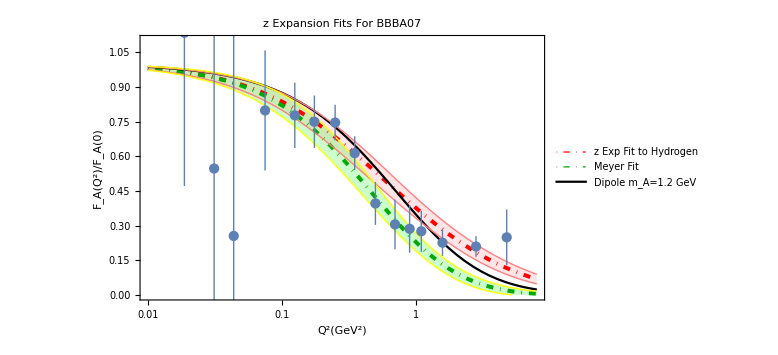

```mathematica
Show[LogLinearPlot[{(zExp[aList,theZ[Q2]] /FA0 /. solution4 /.aMin[[2]]) ,
(zExp[aListMeyer,theZMeyer[Q2]] /FA0 /. solution4Meyer /.meyerCentralValue),
FaDipole/.thisQ2->Q2,
((zExp[aList,theZ[Q2]] /FA0 /. solution4 /.aMin[[2]])+Sqrt[jacobian.covChisq.jacobian ]) ,((zExp[aList,theZ[Q2]] /FA0 /. solution4 /.aMin[[2]])-Sqrt[jacobian.covChisq.jacobian ]),
( (zExp[aListMeyer,theZMeyer[Q2]] /FA0 /. solution4Meyer /.meyerCentralValue) +Sqrt[jacobianMeyer.meyerCovariance.jacobianMeyer ]),((zExp[aListMeyer,theZMeyer[Q2]] /FA0 /. solution4Meyer /.meyerCentralValue) -Sqrt[jacobianMeyer.meyerCovariance.jacobianMeyer ])
 }, {Q2,0.01,8},PlotStyle->{{Thickness[.005],DotDashed,Red},{Thickness[.005],DotDashed,Darker[Green]},{Black},{Thin,Pink},{Thin,Pink},{Thin,Yellow},{Thin,Yellow}},Filling->{4->{{5},Directive[{Opacity[0.2],Pink}]},6->{{7},Directive[{Opacity[0.2],Green}]}},PlotRange->{0,1.1},PlotLegends->Placed[{"z Exp Fit to Hydrogen","Meyer Fit","Dipole m_A=1.2 GeV"},{.75,.8}],LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"Q^2(GeV^2)","F_A(Q^2)/F_A(0)"},ImageSize->Large,PlotLabel->"z Expansion Fits For BBBA07"],ListLogLinearPlot[{dataList}]]
```

### LaTeX Output of Penalized Chi2 fit above

```mathematica
aMin[[2]]
covChisq//TeXForm
```

{a1→1.33574,a2→-1.03582,a3→0.277803,a4→0.064503}

\left(
\begin{array}{cccc}
 0.0341918 & -0.00224855 & -0.169513 & 0.190947 \\
 -0.00224855 & 0.126474 & -0.088693 & -0.30677 \\
 -0.169513 & -0.088693 & 0.945482 & -0.698911 \\
 0.190947 & -0.30677 & -0.698911 & 2.21889 \\
\end{array}
\right)

```mathematica
jacobianZ=D[zExp[aList,z]/FA0 /. solution4,#]&/@freeAs
```

{-0.785978 (-0.25504+z-20.7178 z^5+48.2944 z^6-39.3952 z^7+11.0736 z^8),-0.785978 (-0.280115+z^2-4.31358 z^5+5.78395 z^6-2.38624 z^7+0.195988 z^8),-0.785978 (-0.0752468+z^3-5.78618 z^5+9.46545 z^6-5.97039 z^7+1.36636 z^8),-0.785978 (-0.0457281+z^4-1.43922 z^5-0.401938 z^6+1.48738 z^7-0.600485 z^8)}

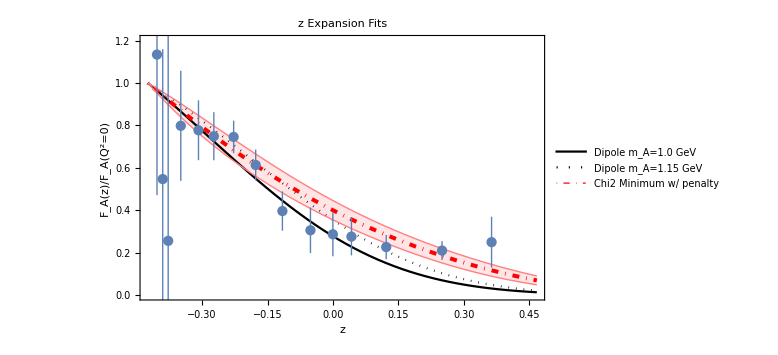

```mathematica
Show[Plot[{1/(1+theQ2byZ[z]/1.00^2)^2,1/(1+theQ2byZ[z]/1.15^2)^2,(zExp[aList,z]/FA0 /. solution4 /.aMin[[2]]),(zExp[aList,z] /FA0 /. solution4 /.aMin[[2]])+Sqrt[jacobianZ.covChisq.jacobianZ ],(zExp[aList,z] /FA0 /. solution4 /.aMin[[2]])-Sqrt[jacobianZ.covChisq.jacobianZ]}, {z,theZ[0],theZ[8]},PlotStyle->{Black,{Dotted,Black},{Thickness[.005],DotDashed,Red},{Thin,Pink},{Thin,Pink}},Filling->{4->{5}},FillingStyle->{Opacity[0.2],Pink},PlotRange->{0,1.2},PlotLegends->Placed[{"Dipole m_A=1.0 GeV","Dipole m_A=1.15 GeV","Chi2 Minimum w/ penalty"},{.7,.7}],LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"z","F_A(z)/F_A(Q^2=0)"},ImageSize->Large,PlotLabel->"z Expansion Fits"],ListPlot[{theZ[#[[1]]],#[[2]]}&/@dataList]]
```

## Proton axial radius from derivative of form factor at zero. This is calculation of r^2 in units of GeV^-2, due to Q^2 derivative so need correction of 0.197 GeV-fm.

```mathematica
axialRadius=Simplify[-D[zExp[aList,theZ[Q2]] /FA0 /. solution4 ,Q2]*6*(.197)^2/.Q2->0]
```

2.44575-1.75723 a1-0.45622 a2-0.311811 a3-0.0928765 a4

```mathematica
axialRadius/.aMin[[2]]
```

0.478497

```mathematica
axialRadiusJacobian=D[axialRadius,#]&/@freeAs
```

{-1.75723,-0.45622,-0.311811,-0.0928765}

### Dependence on lambda for Proton radius

```mathematica
lcurveStudy
```

{{0.00001,{a1→1.44025,a2→-5.23627,a3→-0.122216,a4→23.0826}},{0.0000316228,{a1→1.42496,a2→-5.18696,a3→0.260488,a4→22.2668}},{0.0001,{a1→1.39089,a2→-5.07577,a3→1.10893,a4→20.4468}},{0.000316228,{a1→1.34125,a2→-4.89175,a3→2.32646,a4→17.7034}},{0.001,{a1→1.30246,a2→-4.62703,a3→3.22448,a4→14.9996}},{0.00316228,{a1→1.29075,a2→-4.18037,a3→3.33944,a4→12.4784}},{0.01,{a1→1.29816,a2→-3.44634,a3→2.77075,a4→9.41855}},{0.0316228,{a1→1.3095,a2→-2.52306,a3→1.86368,a4→5.80235}},{0.1,{a1→1.31613,a2→-1.71754,a3→1.04663,a4→2.63887}},{0.316228,{a1→1.32235,a2→-1.24533,a3→0.548748,a4→0.793779}},{1.,{a1→1.33574,a2→-1.03582,a3→0.277803,a4→0.064503}},{3.16228,{a1→1.35516,a2→-0.93075,a3→0.0902356,a4→-0.132866}},{10.,{a1→1.37221,a2→-0.823732,a3→-0.067642,a4→-0.182615}},{31.6228,{a1→1.38459,a2→-0.668895,a3→-0.224247,a4→-0.230957}},{100.,{a1→1.39446,a2→-0.484518,a3→-0.383765,a4→-0.292241}},{316.228,{a1→1.40187,a2→-0.327974,a3→-0.513865,a4→-0.345055}},{1000.,{a1→1.40611,a2→-0.23612,a3→-0.589559,a4→-0.375932}}}

```mathematica
Timing[Sqrt[axialRadiusJacobian.(generalCovChiSq/.lambda->1/.aMin[[2]]).axialRadiusJacobian]]
```

{0.434876,0.155624}

```mathematica
protonRadiusLambdaTable={#[[1]],Around[axialRadius/.#[[2]],Sqrt[axialRadiusJacobian.(generalCovChiSq/.lambda->#[[1]]/.#[[2]]).axialRadiusJacobian]]}&/@lcurveStudy
```

{{0.00001,0.20.9},{0.0000316228,0.20.9},{0.0001,0.00.8},{0.000316228,0.00.7},{0.001,-0.10.5},{0.00316228,-0.10.4},{0.01,0.000.35},{0.0316228,0.180.29},{0.1,0.350.24},{0.316228,0.450.19},{1.,0.480.16},{3.16228,0.470.12},{10.,0.450.09},{31.6228,0.410.06},{100.,0.360.05},{316.228,0.3240.031},{1000.,0.3010.020}}

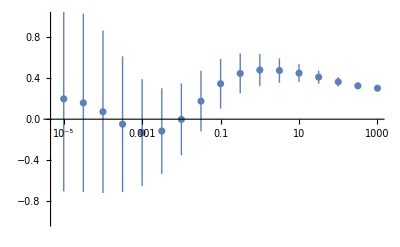

```mathematica
ListLogLinearPlot[protonRadiusLambdaTable,PlotRange->{-1,1}]
```

```mathematica
Around[axialRadius/.aMin[[2]],Sqrt[axialRadiusJacobian.(covChisq/.aMin[[2]]).axialRadiusJacobian]]
```

0.480.16

```mathematica
Sqrt[Around[axialRadius/.aMin[[2]],Sqrt[axialRadiusJacobian.(covChisq/.aMin[[2]]).axialRadiusJacobian]]]
```

0.690.11

```mathematica
protonRadiusLambdaTable//TeXForm
```

\left(
\begin{array}{cc}
 0.00001 & 0.2\pm 0.9 \\
 0.0000316228 & 0.2\pm 0.9 \\
 0.0001 & 0.0\pm 0.8 \\
 0.000316228 & 0.0\pm 0.7 \\
 0.001 & -0.1\pm 0.5 \\
 0.00316228 & -0.1\pm 0.4 \\
 0.01 & 0.00\pm 0.35 \\
 0.0316228 & 0.18\pm 0.29 \\
 0.1 & 0.35\pm 0.24 \\
 0.316228 & 0.45\pm 0.19 \\
 1. & 0.48\pm 0.16 \\
 3.16228 & 0.47\pm 0.12 \\
 10. & 0.45\pm 0.09 \\
 31.6228 & 0.41\pm 0.06 \\
 100. & 0.36\pm 0.05 \\
 316.228 & 0.324\pm 0.031 \\
 1000. & 0.301\pm 0.020 \\
\end{array}
\right)

## Print functions for external export

### Meyer Fit in Q2

```mathematica
Simplify[Sqrt[jacobianMeyer.meyerCovariance.jacobianMeyer ]*Abs[FA0]]//CForm
```

1.2723*Sqrt((2.676043265977421 + 7.887891266775364e-31*Power(Q2,8) - 6.391133649071777*Sqrt(0.1753196 + Q2) + 
       Power(Q2,2)*(117.42843735460404 - 143.48830950595465*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,3)*(167.98419265781618 - 116.73181645952332*Sqrt(0.1753196 + Q2)) + 
       Q2*(30.327134563028242 - 54.20251570430736*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,7)*(1.76807423578193e-28 + 1.2537224710184266e-30*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,6)*(6.7759103375720345e-15 + 1.3652805322741727e-28*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,4)*(42.14737767889076 + 2.803208321734435e-14*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,5)*(-9.910985606529808e-14 + 8.352940728214283e-14*Sqrt(0.1753196 + Q2)))/
     Power(0.6747737373238151 + Sqrt(0.1753196 + Q2),16))

```mathematica
Simplify[zExp[aListMeyer,theZMeyer[Q2]] /. solution4Meyer /.meyerCentralValue]//CForm
```

(-0.4541096590398484 + 1.9539925233402755e-14*Power(Q2,4) - 5.126706276695963*Sqrt(0.1753196 + Q2) + 
     Q2*(-1.4397535998531852 - 23.824184045093943*Sqrt(0.1753196 + Q2)) + 
     Power(Q2,2)*(6.584433052853172 - 1.700329887875803e-13*Sqrt(0.1753196 + Q2)) + 
     Power(Q2,3)*(1.7002232910386852e-13 - 8.348877145181177e-14*Sqrt(0.1753196 + Q2)))/
   Power(0.6747737373238151 + Sqrt(0.1753196 + Q2),8)

### Fit to Tejin’s Hydrogen Data in Q2

```mathematica
Simplify[Sqrt[jacobian.covChisq.jacobian]*Abs[FA0]]//CForm
```

1.2723*Sqrt((186.31883554055463 + 1.2269219238923042e-30*Power(Q2,8) - 444.98106380360593*Sqrt(0.1753196 + Q2) + 
       Power(Q2,2)*(4720.675958490394 - 5058.570136341935*Sqrt(0.1753196 + Q2)) + 
       Q2*(1645.953993948885 - 2661.9378899962317*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,3)*(4603.533331179635 - 2559.771428277622*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,6)*(-4.264139914667114e-14 - 1.8891452360547618e-28*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,7)*(7.402435658377398e-29 - 1.5618313971965055e-29*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,5)*(-7.116459603473659e-13 + 3.4069572712695556e-13*Sqrt(0.1753196 + Q2)) + 
       Power(Q2,4)*(801.0238151006141 + 1.0022887695164681e-12*Sqrt(0.1753196 + Q2)))/
     Power(1.0369761793705528 + Sqrt(0.1753196 + Q2),16))

```mathematica
Simplify[zExp[aList,theZ[Q2]] /. solution4 /.aMin[[2]]]//CForm
```

(-15.952112747143717 - 1.5543122344752192e-15*Power(Q2,4) - 23.168099921629146*Sqrt(0.1753196 + Q2) + 
     Q2*(-79.57110948390732 - 20.05689802052319*Sqrt(0.1753196 + Q2)) + 
     Power(Q2,2)*(-53.92271519250546 - 8.619941878461974e-14*Sqrt(0.1753196 + Q2)) + 
     Power(Q2,3)*(3.0884417533562175e-14 - 1.7763568394002505e-15*Sqrt(0.1753196 + Q2)))/
   Power(1.0369761793705528 + Sqrt(0.1753196 + Q2),8)

### Fit to Tejin’s Hydrogen Data in z

```mathematica
Simplify[Sqrt[jacobianZ.covChisq.jacobianZ]*Abs[FA0]]//CForm
```

1.2723*Sqrt(0.0020754897125583507 - 0.005024555742936879*z + 0.0036374987029649634*Power(z,2) + 
     0.03291880955129803*Power(z,3) - 0.14569212751091273*Power(z,4) + 0.12001194750684094*Power(z,5) + 
     0.21400772672844015*Power(z,6) - 0.3484277246162543*Power(z,7) + 0.4928928089792781*Power(z,8) - 
     1.6796081261483682*Power(z,9) + 2.5718646385352235*Power(z,10) - 1.4726015426434733*Power(z,11) + 
     0.4457993325590239*Power(z,12) - 1.0878196235747661*Power(z,13) + 1.5153944682521463*Power(z,14) - 
     0.817355746253383*Power(z,15) + 0.1579267259623206*Power(z,16))

```mathematica
Simplify[zExp[aList,z] /. solution4 /.aMin[[2]]]//CForm
```

-0.5083074453938297 + 1.3357366733598786*z - 1.035824376021557*Power(z,2) + 0.2778031607873682*Power(z,3) + 
   0.06450296119646338*Power(z,4) - 0.6051225577696828*Power(z,5) + 0.3698222690497177*Power(z,6) + 
   0.35994459224774156*Power(z,7) - 0.2585552774561013*Power(z,8)

### Print aMin

```mathematica
aList/.solution4/.aMin[[2]]
```

{-0.508307,1.33574,-1.03582,0.277803,0.064503,-0.605123,0.369822,0.359945,-0.258555}

```mathematica
Around[freeAs/.aMin[[2]],Sqrt[Diagonal[covChisq]]]
```

{1.33574{0.18491,0.355632,0.972359,1.4896},-1.03582{0.18491,0.355632,0.972359,1.4896},0.277803{0.18491,0.355632,0.972359,1.4896},0.064503{0.18491,0.355632,0.972359,1.4896}}

```mathematica
SetPrecision[covChisq,2]//TeXForm
```

\left(
\begin{array}{cccc}
 0.034 & -0.0022 & -0.17 & 0.19 \\
 -0.0022 & 0.13 & -0.089 & -0.31 \\
 -0.17 & -0.089 & 0.95 & -0.70 \\
 0.19 & -0.31 & -0.70 & 2.2 \\
\end{array}
\right)

```mathematica
Sqrt[Diagonal[covChisq]][[2]]^2
```

0.126474

### C & Python Forms of chiSq, zExp prediction, etc for external fits

Here is the chi2

```mathematica
assign={a1->1.3357366733598786,a2->-1.035824376021557,a3->0.2778031607873682,a4->0.06450296119646338,lambda->1}
chiSq/.assign
```

{a1→1.33574,a2→-1.03582,a3→0.277803,a4→0.064503,lambda→1}

9.27063

```mathematica
Simplify[chiSq]//CForm
```

(186.1860923809743 + 34.670139771992176*Power(a1,4) + 33.27026238989032*Power(a2,4) + 68.17982273698937*a3 + 
     13.708576984906905*Power(a3,2) + 2.487123584342667*Power(a3,3) + 0.20623086980845043*Power(a3,4) + 
     47.70927499132658*a4 + 19.12310948266784*a3*a4 + 4.821875422256927*Power(a3,2)*a4 + 
     0.5098817903941941*Power(a3,3)*a4 + 6.635925783523673*Power(a4,2) + 3.131862058601409*a3*Power(a4,2) + 
     0.4749263294087737*Power(a3,2)*Power(a4,2) + 0.680685819930702*Power(a4,3) + 0.19746050151985195*a3*Power(a4,3) + 
     0.030909911206449862*Power(a4,4) + Power(a1,3)*
      (48.4735759547176 + 102.0608589465198*a2 + 29.9798380885572*a3 + 17.046125510273875*a4) + 
     Power(a2,3)*(123.89903850743222 + 37.02065072461622*a3 + 23.20851638277183*a4) + 7262.824636922534*lambda - 
     2006.159079203825*a3*lambda + 146.44638422262582*Power(a3,2)*lambda + 215.65362845914044*a4*lambda - 
     20.48609848494572*a3*a4*lambda + 5.2659823127548435*Power(a4,2)*lambda + 
     Power(a2,2)*(221.92681607205327 + 15.545046737852616*Power(a3,2) + 65.40491143928793*a4 + 
        6.077389865354891*Power(a4,2) + a3*(99.6986530983255 + 19.394315491683706*a4) + 48.60603135566903*lambda) + 
     Power(a1,2)*(-71.83861593175915 + 126.30290559462398*Power(a2,2) + 11.005696146377838*Power(a3,2) + 
        14.85386253094298*a4 + 3.730462173850529*Power(a4,2) + a3*(27.44280236400086 + 12.782855546221091*a4) + 
        a2*(82.30409111406917 + 74.5418096837744*a3 + 43.312499910986126*a4) + 4393.635813517758*lambda) + 
     a2*(290.3334235933162 + 2.9170329987970396*Power(a3,3) + 11.544965499347661*Power(a4,2) + 
        0.7077039105587835*Power(a4,3) + Power(a3,2)*(27.099786613523097 + 5.433202520930326*a4) + 
        a4*(76.42193035121784 - 5.408272336597099*lambda) - 1060.1589070293787*lambda + 
        a3*(109.61497273184845 + 35.30196544642648*a4 + 3.3890600193341043*Power(a4,2) + 162.84685140818382*lambda)) + 
     a1*(17.640995249301824 + 91.83110039373736*Power(a2,3) + 2.2268374636811865*Power(a3,3) + 3.9659585038374594*a4 + 
        4.901341508795532*Power(a4,2) + 0.49310327572152335*Power(a4,3) + 
        Power(a3,2)*(12.30696637268208 + 4.015792368102464*a4) + 
        Power(a2,2)*(144.73026269817728 + 79.4125386559945*a3 + 48.139078841435236*a4) - 11290.182074822971*lambda - 
        159.89472528992673*a4*lambda + a2*(15.21504875851133 + 22.99547674845958*Power(a3,2) + 53.11418688226629*a4 + 
           8.431895602786877*Power(a4,2) + a3*(83.47893280052126 + 27.752858908271048*a4) + 838.0826448271216*lambda) + 
        a3*(-0.02565840076005088 + 15.39470074825567*a4 + 2.4294527979566767*Power(a4,2) + 1571.679269347251*lambda)))/
   Power(1.7014522229967783 + 1.*a1 + 1.0983179435499004*a2 + 0.2950395095657635*a3 + 0.17929811192654405*a4,2)

```mathematica
Simplify[chiSq]//FortranForm
```

(186.1860923809743 + 34.670139771992176*a1**4 + 33.27026238989032*a2**4 + 68.17982273698937*a3 + 
     -    13.708576984906905*a3**2 + 2.487123584342667*a3**3 + 0.20623086980845043*a3**4 + 47.70927499132658*a4 + 
     -    19.12310948266784*a3*a4 + 4.821875422256927*a3**2*a4 + 0.5098817903941941*a3**3*a4 + 6.635925783523673*a4**2 + 
     -    3.131862058601409*a3*a4**2 + 0.4749263294087737*a3**2*a4**2 + 0.680685819930702*a4**3 + 
     -    0.19746050151985195*a3*a4**3 + 0.030909911206449862*a4**4 + 
     -    a1**3*(48.4735759547176 + 102.0608589465198*a2 + 29.9798380885572*a3 + 17.046125510273875*a4) + 
     -    a2**3*(123.89903850743222 + 37.02065072461622*a3 + 23.20851638277183*a4) + 7262.824636922534*lambda - 
     -    2006.159079203825*a3*lambda + 146.44638422262582*a3**2*lambda + 215.65362845914044*a4*lambda - 
     -    20.48609848494572*a3*a4*lambda + 5.2659823127548435*a4**2*lambda + 
     -    a2**2*(221.92681607205327 + 15.545046737852616*a3**2 + 65.40491143928793*a4 + 6.077389865354891*a4**2 + 
     -       a3*(99.6986530983255 + 19.394315491683706*a4) + 48.60603135566903*lambda) + 
     -    a1**2*(-71.83861593175915 + 126.30290559462398*a2**2 + 11.005696146377838*a3**2 + 14.85386253094298*a4 + 
     -       3.730462173850529*a4**2 + a3*(27.44280236400086 + 12.782855546221091*a4) + 
     -       a2*(82.30409111406917 + 74.5418096837744*a3 + 43.312499910986126*a4) + 4393.635813517758*lambda) + 
     -    a2*(290.3334235933162 + 2.9170329987970396*a3**3 + 11.544965499347661*a4**2 + 0.7077039105587835*a4**3 + 
     -       a3**2*(27.099786613523097 + 5.433202520930326*a4) + a4*(76.42193035121784 - 5.408272336597099*lambda) - 
     -       1060.1589070293787*lambda + a3*(109.61497273184845 + 35.30196544642648*a4 + 3.3890600193341043*a4**2 + 
     -          162.84685140818382*lambda)) + a1*(17.640995249301824 + 91.83110039373736*a2**3 + 
     -       2.2268374636811865*a3**3 + 3.9659585038374594*a4 + 4.901341508795532*a4**2 + 0.49310327572152335*a4**3 + 
     -       a3**2*(12.30696637268208 + 4.015792368102464*a4) + 
     -       a2**2*(144.73026269817728 + 79.4125386559945*a3 + 48.139078841435236*a4) - 11290.182074822971*lambda - 
     -       159.89472528992673*a4*lambda + a2*(15.21504875851133 + 22.99547674845958*a3**2 + 53.11418688226629*a4 + 
     -          8.431895602786877*a4**2 + a3*(83.47893280052126 + 27.752858908271048*a4) + 838.0826448271216*lambda) + 
     -       a3*(-0.02565840076005088 + 15.39470074825567*a4 + 2.4294527979566767*a4**2 + 1571.679269347251*lambda)))/
     -  (1.7014522229967783 + 1.*a1 + 1.0983179435499004*a2 + 0.2950395095657635*a3 + 0.17929811192654405*a4)**2

Here is the prediction for F_A(Q^2)/F_A(0)

```mathematica
zExp[aList,theZ[Q2]] /FA0/. solution4//CForm
```

-0.7859781498074354*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
     0.045728129215033365*a4 + ((-15.187822779972839 + 11.073611956483601*a1 + 0.19598784071665049*a2 + 
          1.3663628494472262*a3 - 0.6004845225261678*a4)*Power(-1.0369761793705528 + Sqrt(0.1753196 + Q2),8))/
      Power(1.0369761793705528 + Sqrt(0.1753196 + Q2),8) + 
     ((52.07253524562117 - 39.395240993658064*a1 - 2.3862440253142303*a2 - 5.97038691239049*a3 + 1.4873755058040041*a4)*
        Power(-1.0369761793705528 + Sqrt(0.1753196 + Q2),7))/Power(1.0369761793705528 + Sqrt(0.1753196 + Q2),7) + 
     ((-60.751291119891356 + 48.294447825934405*a1 + 5.783951362866602*a2 + 9.465451397788906*a3 - 0.4019380901046714*a4)*
        Power(-1.0369761793705528 + Sqrt(0.1753196 + Q2),6))/Power(1.0369761793705528 + Sqrt(0.1753196 + Q2),6) + 
     ((24.300516447956543 - 20.717779130373764*a1 - 4.313580545146641*a2 - 5.786180559115562*a3 - 1.4392247639581315*a4)*
        Power(-1.0369761793705528 + Sqrt(0.1753196 + Q2),5))/Power(1.0369761793705528 + Sqrt(0.1753196 + Q2),5) + 
     (a4*Power(-1.0369761793705528 + Sqrt(0.1753196 + Q2),4))/Power(1.0369761793705528 + Sqrt(0.1753196 + Q2),4) + 
     (a3*Power(-1.0369761793705528 + Sqrt(0.1753196 + Q2),3))/Power(1.0369761793705528 + Sqrt(0.1753196 + Q2),3) + 
     (a2*Power(-1.0369761793705528 + Sqrt(0.1753196 + Q2),2))/Power(1.0369761793705528 + Sqrt(0.1753196 + Q2),2) + 
     (a1*(-1.0369761793705528 + Sqrt(0.1753196 + Q2)))/(1.0369761793705528 + Sqrt(0.1753196 + Q2)))

```mathematica
zExp[aList,theZ[Q2]] /FA0/. solution4//FortranForm
```

-0.7859781498074354*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 
     -    0.07524677573007925*a3 - 0.045728129215033365*a4 + 
     -    ((-15.187822779972839 + 11.073611956483601*a1 + 0.19598784071665049*a2 + 1.3663628494472262*a3 - 
     -         0.6004845225261678*a4)*(-1.0369761793705528 + Sqrt(0.1753196 + Q2))**8)/
     -     (1.0369761793705528 + Sqrt(0.1753196 + Q2))**8 + 
     -    ((52.07253524562117 - 39.395240993658064*a1 - 2.3862440253142303*a2 - 5.97038691239049*a3 + 
     -         1.4873755058040041*a4)*(-1.0369761793705528 + Sqrt(0.1753196 + Q2))**7)/
     -     (1.0369761793705528 + Sqrt(0.1753196 + Q2))**7 + 
     -    ((-60.751291119891356 + 48.294447825934405*a1 + 5.783951362866602*a2 + 9.465451397788906*a3 - 
     -         0.4019380901046714*a4)*(-1.0369761793705528 + Sqrt(0.1753196 + Q2))**6)/
     -     (1.0369761793705528 + Sqrt(0.1753196 + Q2))**6 + 
     -    ((24.300516447956543 - 20.717779130373764*a1 - 4.313580545146641*a2 - 5.786180559115562*a3 - 
     -         1.4392247639581315*a4)*(-1.0369761793705528 + Sqrt(0.1753196 + Q2))**5)/
     -     (1.0369761793705528 + Sqrt(0.1753196 + Q2))**5 + 
     -    (a4*(-1.0369761793705528 + Sqrt(0.1753196 + Q2))**4)/(1.0369761793705528 + Sqrt(0.1753196 + Q2))**4 + 
     -    (a3*(-1.0369761793705528 + Sqrt(0.1753196 + Q2))**3)/(1.0369761793705528 + Sqrt(0.1753196 + Q2))**3 + 
     -    (a2*(-1.0369761793705528 + Sqrt(0.1753196 + Q2))**2)/(1.0369761793705528 + Sqrt(0.1753196 + Q2))**2 + 
     -    (a1*(-1.0369761793705528 + Sqrt(0.1753196 + Q2)))/(1.0369761793705528 + Sqrt(0.1753196 + Q2)))

Here is the chi2 penalty term

```mathematica
penaltyTerm//CForm
```

(Power(a1,2)/(25.*Power(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
          0.045728129215033365*a4,2)) + Power(a2,2)/
      (25.*Power(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
          0.045728129215033365*a4,2)) + Power(a3,2)/
      (25.*Power(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
          0.045728129215033365*a4,2)) + Power(24.300516447956543 - 20.717779130373764*a1 - 4.313580545146641*a2 - 
        5.786180559115562*a3 - 1.4392247639581315*a4,2)/
      (25.*Power(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
          0.045728129215033365*a4,2)) + (64*Power(-15.187822779972839 + 11.073611956483601*a1 + 0.19598784071665049*a2 + 
          1.3663628494472262*a3 - 0.6004845225261678*a4,2))/
      (625.*Power(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
          0.045728129215033365*a4,2)) + (36*Power(-60.751291119891356 + 48.294447825934405*a1 + 5.783951362866602*a2 + 
          9.465451397788906*a3 - 0.4019380901046714*a4,2))/
      (625.*Power(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
          0.045728129215033365*a4,2)) + Power(a4,2)/
      (25.*Power(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
          0.045728129215033365*a4,2)) + (49*Power(52.07253524562117 - 39.395240993658064*a1 - 2.3862440253142303*a2 - 
          5.97038691239049*a3 + 1.4873755058040041*a4,2))/
      (625.*Power(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
          0.045728129215033365*a4,2)))*lambda

```mathematica
penaltyTerm//FortranForm
```

(a1**2/(25.*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
     -          0.045728129215033365*a4)**2) + a2**2/
     -     (25.*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
     -          0.045728129215033365*a4)**2) + a3**2/
     -     (25.*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
     -          0.045728129215033365*a4)**2) + (24.300516447956543 - 20.717779130373764*a1 - 4.313580545146641*a2 - 
     -        5.786180559115562*a3 - 1.4392247639581315*a4)**2/
     -     (25.*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
     -          0.045728129215033365*a4)**2) + (64*
     -       (-15.187822779972839 + 11.073611956483601*a1 + 0.19598784071665049*a2 + 1.3663628494472262*a3 - 
     -          0.6004845225261678*a4)**2)/
     -     (625.*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
     -          0.045728129215033365*a4)**2) + (36*
     -       (-60.751291119891356 + 48.294447825934405*a1 + 5.783951362866602*a2 + 9.465451397788906*a3 - 
     -          0.4019380901046714*a4)**2)/
     -     (625.*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
     -          0.045728129215033365*a4)**2) + a4**2/
     -     (25.*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
     -          0.045728129215033365*a4)**2) + (49*
     -       (52.07253524562117 - 39.395240993658064*a1 - 2.3862440253142303*a2 - 5.97038691239049*a3 + 
     -          1.4873755058040041*a4)**2)/
     -     (625.*(-0.4339377937135097 - 0.2550396583861828*a1 - 0.28011463312238144*a2 - 0.07524677573007925*a3 - 
     -          0.045728129215033365*a4)**2))*lambda